## cluster model - (1)

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[λ, e]=0.1;α=0.1;β=0.6;Subscript[λ, γ]=0.1;Subscript[λ, γb]=0.03;Subscript[n, EB]=100;
```

```mathematica
sol=DSolve[{
ecad'[t]==α EB[t]+Subscript[λ, e] ecad[t] ,
EB'[t]==-α EB[t] -β EB[t]+Subscript[λ, γ] EB[t],
B'[t]==β*EB[t]+Subscript[λ, γb] B[t],
B[0]==0,ecad[0]==1,EB[0]==Subscript[n, EB]
},{ecad,EB,B},t
]
```

{{B→Function[{t},95.2381 ⅇ^(-0.6 t) (-1.+1. ⅇ^(0.63 t))],EB→Function[{t},100. ⅇ^(-0.6 t)],ecad→Function[{t},1. ⅇ^(-0.6 t) (-14.2857+15.2857 ⅇ^(0.7 t))]}}

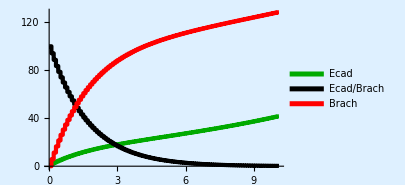

```mathematica
ListStepPlot[Thread[{Range[0,10,0.1],#}]&/@Transpose@Table[{First[(ecad/.sol)][t],First[(EB/.sol)][t],First[(B/.sol)][t]},{t,0,10,0.1}],PlotStyle->{{Thickness[0.01],Darker@Green},{Thickness[0.01],Black},{Thickness[0.01],Red}},Background->LightBlue,PlotLegends->{"Ecad","Ecad/Brach","Brach"},
ImageSize->300]
```

## cluster model - (2)

```mathematica
ClearAll["Global`*"];
```

```mathematica
(* 
β -> conversion of EB to B;
α -> conversion of EB to E;
Subscript[λ, e] -> growth-rate of E;
Subscript[λ, γ] -> growth-rate of EB;
Subscript[λ, B] -> growth-rate of B
*)
```

```mathematica
α=0.075;β=0.5;Subscript[n, EB]=100;
```

```mathematica
DiffEqns={ecad'[t]==α EB[t]+Subscript[λ, ecad][t] ecad[t],
EB'[t]==-α EB[t]-β EB[t]+Subscript[λ, EB][t] EB[t],
B'[t]==β EB[t]+Subscript[λ, B][t] B[t]};
```

```mathematica
icns={B[0]==0,ecad[0]==1,EB[0]==Subscript[n, EB],Subscript[λ, EB][0]==0.1,Subscript[λ, B][0]==0.005,Subscript[λ, ecad][0]==0.1};
```

```mathematica
sol=NDSolve[{DiffEqns,icns,WhenEvent[EB[t]<1,{Subscript[λ, EB][t]->0,Subscript[λ, B][t]->0.005,Subscript[λ, ecad][t]-> 0.01,EB[t]-> 0}]},
{ecad,EB,B},{t,0,50,0.1},DiscreteVariables->{Subscript[λ, EB],Subscript[λ, B],Subscript[λ, ecad]}
]
```

{{ecad→InterpolatingFunction[…],EB→InterpolatingFunction[…],B→InterpolatingFunction[…]}}

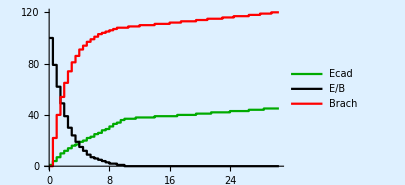

```mathematica
ListStepPlot[Thread[{Range[0,30,0.5],#}]&/@Transpose@Table[Round@{First[(ecad/.sol)][t],First[(EB/.sol)][t],First[(B/.sol)][t]},{t,0,30,0.5}],
PlotStyle->{{Thick,Darker@Green},{Thick,Black},{Thick,Red}},Background->LightBlue,PlotLegends->{"Ecad","E/B","Brach"},
ImageSize->300,AxesStyle->Thick,TicksStyle->Directive[Black,Thick,Italic]
]
```

## cluster model - (non elongating tip)

```mathematica
ClearAll["Global`*"];
```

```mathematica
(* 
β -> conversion of EB to B; α -> conversion of EB to E;
Subscript[λ, ecad] -> growth-rate of E; Subscript[λ, EB] -> growth-rate of EB;
Subscript[λ, B] -> growth-rate of B *)
```

```mathematica
α=0.05;β=0.1;Subscript[n, EB]=100;Subscript[n, B]=25;Subscript[n, e]=2;
```

```mathematica
DiffEqns={
ecad'[t]==α  EB[t]+Subscript[λ, ecad][t] ecad[t],
EB'[t]==-α EB[t]-β EB[t]+Subscript[λ, EB][t] EB[t],
B'[t]==β EB[t]+Subscript[λ, B][t] B[t]
};
```

```mathematica
icns={B[0]==Subscript[n, B],ecad[0]==Subscript[n, e],EB[0]==Subscript[n, EB],
Subscript[λ, EB][0]==0.04,Subscript[λ, B][0]==0.04,Subscript[λ, ecad][0]==0.04};
```

```mathematica
sol=NDSolve[{DiffEqns,icns,WhenEvent[EB[t]<2,{Subscript[λ, EB][t]->0.05,Subscript[λ, B][t]->0.04,Subscript[λ, ecad][t]-> 0.04,EB[t]-> 0}],
WhenEvent[t>15,{Subscript[λ, B][t]->-0.5,Subscript[λ, ecad][t]->- 0.25}]},
{ecad,EB,B},{t,0,50,0.1},DiscreteVariables->{Subscript[λ, EB],Subscript[λ, B],Subscript[λ, ecad]}]
```

{{ecad→InterpolatingFunction[…],EB→InterpolatingFunction[…],B→InterpolatingFunction[…]}}

```mathematica
res=Thread[{Range[0,35,0.5],#}]&/@Transpose@Table[Round@{First[(ecad/.sol)][t],
First[(EB/.sol)][t],First[(B/.sol)][t]},{t,0,35,0.5}];
```

```mathematica
Image[
Rasterize[ListStepPlot[res,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Darker@Blue}},Background->LightBlue,PlotLegends->{"Ecad cluster population","Ecad/Brach pool","Brachyury alone"},ImageSize->300,AxesStyle->Thick,TicksStyle->Directive[Black,Thick,Italic],
PlotRange->Full,Filling->Bottom,Axes->{False,True}],
"Image",ImageResolution->500],
ImageSize->400]
```

-Graphics-

```mathematica
Image[
Rasterize[ListLogPlot[res,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Darker@Blue}},Background->LightBlue,PlotLegends->{"Ecad cluster population","Ecad/Brach pool","Brachyury alone"},ImageSize->300,AxesStyle->Thick,TicksStyle->Directive[Black,Thick,Italic],PlotRange->Full,Filling->Bottom,Axes->{False,True}],
"Image",ImageResolution->500],
ImageSize->400]
```

-Graphics-

## cluster model - (elongating tip)

```mathematica
ClearAll["Global`*"];
```

```mathematica
(* 
β -> conversion of EB to B; α -> conversion of EB to E;
Subscript[λ, ecad] -> growth-rate of E; Subscript[λ, EB] -> growth-rate of EB;
Subscript[λ, B] -> growth-rate of B *)
```

```mathematica
α=0.05;β=0.1;Subscript[n, EB]=600;Subscript[n, B]=150;Subscript[n, e]=8;
```

```mathematica
DiffEqns={
ecad'[t]==α  EB[t]+Subscript[λ, ecad][t] ecad[t],
EB'[t]==-α EB[t]-β EB[t]+Subscript[λ, EB][t] EB[t],
B'[t]==β EB[t]+Subscript[λ, B][t] B[t]
};
```

```mathematica
icns={B[0]==Subscript[n, B],ecad[0]==Subscript[n, e],EB[0]==Subscript[n, EB],
Subscript[λ, EB][0]==0.04,Subscript[λ, B][0]==0.04,Subscript[λ, ecad][0]==0.04};
```

```mathematica
sol=NDSolve[{DiffEqns,icns,WhenEvent[EB[t]<1,{Subscript[λ, EB][t]->0.05,Subscript[λ, B][t]->0.04,Subscript[λ, ecad][t]-> 0.04,EB[t]-> 0}],
WhenEvent[t>15,{Subscript[λ, B][t]->-0.50,Subscript[λ, ecad][t]->- 0.25}]},
{ecad,EB,B},{t,0,50,0.1},DiscreteVariables->{Subscript[λ, EB],Subscript[λ, B],Subscript[λ, ecad]}]
```

{{ecad→InterpolatingFunction[…],EB→InterpolatingFunction[…],B→InterpolatingFunction[…]}}

```mathematica
res=Thread[{Range[0,35,0.5],#}]&/@Transpose@Table[Round@{First[(ecad/.sol)][t],
First[(EB/.sol)][t],First[(B/.sol)][t]},{t,0,35,0.5}];
```

```mathematica
Image[
Rasterize[ListStepPlot[res,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Darker@Blue}},Background->LightBlue,PlotLegends->{"Ecad cluster population","Ecad/Brach pool","Brachyury alone"},ImageSize->300,AxesStyle->Thick,TicksStyle->Directive[Black,Thick,Italic],PlotRange->All,Filling->Bottom,Axes->{False,True}],
"Image",ImageResolution->500],
ImageSize->400]
```

-Graphics-

```mathematica
Image[
Rasterize[ListLogPlot[res,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Darker@Blue}},Background->LightBlue,PlotLegends->{"Ecad cluster population","Ecad/Brach pool","Brachyury alone"},ImageSize->300,AxesStyle->Thick,TicksStyle->Directive[Black,Thick,Italic],PlotRange->All,Filling->Bottom,Axes->{False,True}],
"Image",ImageResolution->500],
ImageSize->400]
```

-Graphics-